## Adiabatic Bouncer model

-Graphics-

```mathematica
kernel=$ProcessorCount;
```

```mathematica
NextPointC=Compile[{{NIter,_Integer},{ϕ0,_Real},{vy0,_Real},{ζ,_Real},{z,_Real}},Module[{ϕn,vyn,ϕn0=Mod[ϕ0,2 π],vyn0=vy0,PS},
PS=Table[{0.,0.},{NIter}];;
Do[ϕn=ϕn0+2 vyn0;vyn=Abs[ (vyn0+ζ/vyn0^(z-1)*Sin[ϕn])];PS[[i]]={Mod[ϕn,2π],vyn};(*Aqui coloquei para armazenar vyn*)
ϕn0=ϕn;vyn0=vyn,{i,1,NIter}];PS]];
```

```mathematica
VrmsC[NIter_,Ein_,ζ_,z_]:=Module[{data,transp1,dataT,points,meanV},max=Sum[1,{i,0.1,2 π,0.0025}];
d=0;
Print[Dynamic[Row[{Round[100 d/max,0.1],"% done!"}]]];
LaunchKernels[kernel];
DistributeDefinitions[d];
SetSharedVariable[d];
data=ParallelTable[d++;points=NextPointC[NIter,i,Ein+i-π,ζ,z];Table[points[[ii]],{ii,1000,Length[points],1000}],{i,0.1,2 π,0.002}];
transp1=Table[Transpose[data[[i]]][[2]],{i,1,Length[data]}];
dataT=Transpose[transp1];
meanV=Table[RootMeanSquare[dataT[[i]]],{i,1,Length[dataT]}];
CloseKernels[];
meanV];
```

```mathematica
(*Number of initial condictions*)
Sum[1,{i,0.1,2 π,0.002}]
```

3092

```mathematica
VrmsFunc[NIter_,z_,ζ_]:=Module[{Zet,Z,Vrms,fileNames,test,meanVBouc,normalVBouc},Zet=StringJoin[DeleteCases[StringSplit[ToString[ζ],""],"."]];Z=StringJoin[DeleteCases[StringSplit[ToString[z],""],"."]];Vrms=StringJoin["Vrms-",Zet,"-",Z,".txt"];fileNames=FileNames[Vrms,{StringJoin["Dados-",Vrms]}];test={};test=Quiet[ToExpression[Import[fileNames[[1]]]][[1]]];meanVBouc=test;If[Quiet[test==$Failed[[1]]],Clear[meanVBouc];
meanVBouc=VrmsC[NIter,10.,ζ,z];
meanVBouc=Table[{i*1000,meanVBouc[[i]]},{i,1,Length[meanVBouc]}];];normalVBouc=Table[{meanVBouc[[i]][[1]],meanVBouc[[i]][[2]]/meanVBouc[[1]][[2]]},{i,1,Length[meanVBouc]}];If[Quiet[test==$Failed[[1]]],
CreateDirectory[StringJoin[NOME,"Dados-",Vrms]];SetDirectory[StringJoin[NOME,"Dados-",Vrms]] ;Export[Vrms,InputForm[meanVBouc]];];normalVBouc]
```

## Phase Space

PhasSpacC[NIter,Ein,ζ,z,ini,step]
NIter = number of iterations
Ein = initial energy (speed)
ζ parameter
z parameter
ini = discards initial ini iterations (transient region)
step = saves the iteration points separated by step (avoids overloading the figure)

## Find Directory

```mathematica
NOME=NotebookDirectory[]; (* Find directory where this notebook is placed *)
```

```mathematica
SetDirectory[NOME];
```

## Root mean square of velocities using ζ̄=5

### z=0.429and ζ̄=5

```mathematica
z=0.429;ζ=5.;
```

```mathematica
(*If the data has already been calculated,the command only reads it,otherwise the subroutines generate new data according to the values ​​of z and zeta.*)SetDirectory[NOME];
pontosBouc0429=VrmsFunc[1000000,z,ζ];
```

```mathematica
(*Fit the data using n^(1/2z)*)
f0429[n_]=a n^(b/(2 z))/.FindFit[pontosBouc0429[[1;;10]],a n^(b/(2 z)),{a,b},n];
```

### z=0.9 and ζ̄=5

```mathematica
z=0.9;ζ=5.;
```

```mathematica
(*If the data has already been calculated,the command only reads it,otherwise the subroutines generate new data according to the values ​​of z and zeta.*)SetDirectory[NOME];
pontosBouc09=VrmsFunc[1000000,z,ζ];
```

```mathematica
(*Fit the data using n^(1/2z)*)
f09[n_]=a n^(1/(2 z))/.FindFit[pontosBouc09[[50;;100]],a n^(1/(2 z)),{a},n];
```

### z=1.0 and ζ̄=5

```mathematica
z=1.;ζ=5.;
```

```mathematica
(*If the data has already been calculated,the command only reads it,otherwise the subroutines generate new data according to the values ​​of z and zeta.*)SetDirectory[NOME];
pontosBouc1=VrmsFunc[1000000,z,ζ];
```

```mathematica
(*Fit the data using n^(1/2z)*)
Clear[f1];f1[n_]=a n^(1/(2 z))/.FindFit[pontosBouc1[[10;;100]],a n^(1/(2 z)),{a},n];
```

### z=1.1 and ζ̄=5

```mathematica
z=1.1;ζ=5.;
```

```mathematica
(*If the data has already been calculated,the command only reads it,otherwise the subroutines generate new data according to the values ​​of z and zeta.*)SetDirectory[NOME];
pontosBouc11=VrmsFunc[1000000,z,ζ];
```

```mathematica
(*Fit the data using n^(1/2z)*)
Clear[f11];f11[n_]=a n^(0.9/(2 z))/.FindFit[pontosBouc11[[10;;100]],a n^(0.9/(2 z)),{a},n];
```

### graphics

```mathematica
fits={f0429[n],f09[n],f1[n],f11[n]}
```

{0.00200239 n^0.906712,0.0226439 n^0.555556,0.0314871 n^0.5,0.0574963 n^0.409091}

```mathematica
(1/(Exponent[fits,n]))/2
```

{0.551443,0.9,1.,1.22222}

```mathematica
legends={"∼ n^(1/(2×0.55))","∼ n^(1/(2×0.9))","∼ n^(1/2)","∼ n^(1/(2×1.2))"};
```

```mathematica
fig1b=LogLogPlot[{f0429[n],f09[n],f1[n],f11[n]},{n,1000,1000000},PlotRange->{{900,1000100},{0.3,5000}},Frame->True,FrameStyle->Directive[Black,FontSize->16],PlotStyle->{{Darker[Green]},{Dashed,Orange},{DotDashed,Red},{Dotted,Darker[Blue]}},FrameLabel->{Style["n",FontSize->17],Style["V_rms^(z)",FontSize->17]},LabelStyle->Directive[Black,FontSize->15],PlotLegends->Placed[legends,{{0.14,0.67}}],FrameTicks->{{{1,10,100,1000},None},{{1000,10000,100000,1000000},None}},AspectRatio->3/5,ImageSize->500];
```

```mathematica
pontosBouc1Fig=Table[pontosBouc0429[[i]],{i,1,1000,1}];pontosBouc2Fig=Table[pontosBouc09[[i]],{i,1,1000,2}];pontosBouc3Fig=Table[pontosBouc1[[i]],{i,1,1000,2}];pontosBouc4Fig=Table[pontosBouc11[[i]],{i,1,1000,2}];
```

```mathematica
legends={"V_rms^(z = 0.4)","V_rms^(z = 0.9)","V_rms^(z = 1.0)","V_rms^(z = 1.1)"};
```

```mathematica
fig1c=ListLogLogPlot[{pontosBouc1Fig,pontosBouc2Fig,pontosBouc3Fig,pontosBouc4Fig},PlotMarkers->{"□","△","◇","◦"},PlotStyle->{{Darker[Green]},{Orange},{Red},{Darker[Blue]}},Frame->True,FrameStyle->Directive[Black,FontSize->16],PlotRange->{{900,1000100},{0.3,5000}},FrameLabel->{Style["n",FontSize->17],Style["V_rms^(z)",FontSize->17]},LabelStyle->Directive[Black,FontSize->15.5],PlotLegends->Placed[legends,{{0.36,0.69}}],FrameTicks->{{{0.1,1,10,10^2,10^3},None},{{1000,10^4,10^5,10^6},None}},AspectRatio->3/5,ImageSize->500];
```

```mathematica
Show[{fig1b,fig1c}]
```

-Graphics-

## Dependence of final velocities with z using ζ̄=5

### z = 0.55; This is the critical z for ζ = 5.

```mathematica
ζ=5.;z=0.55;SetDirectory[NOME];pontosBouc=VrmsFunc[3000000,z,ζ];
```

Graphic normalized by n: (<V_n>)/n

```mathematica
pontosBoucN=Table[{pontosBouc[[i]][[1]],(pontosBouc[[i]][[2]])/(√(pontosBouc[[i]][[1]]))},{i,1,Length[pontosBouc]}];
```

```mathematica
ListLogLogPlot[{pontosBoucN},PlotMarkers->{"◦"},PlotStyle->GrayLevel[0.2],Frame->True,PlotRange->All,FrameLabel->{Style["n",FontSize->18],Style["V_rms^(z)/√n",FontSize->18]},Ticks->{{1000,10^4,10^5,10^6},{0.01,0.05,0.1,0.15,0.2}},LabelStyle->Directive[Black,FontSize->19],ImageSize->610]
```

-Graphics-

### For z = 0.56, 0.57, ...,0.6 we still have large fluctuations for V_∞

```mathematica
ζ=5.;z=0.57;SetDirectory[NOME];pontosBouc=VrmsFunc[3000000,z,ζ];
```

Graphic normalized by n: (<V_n>)/n

```mathematica
pontosBoucN=Table[{pontosBouc[[i]][[1]],(pontosBouc[[i]][[2]])/(√(pontosBouc[[i]][[1]]))},{i,1,Length[pontosBouc]}];
```

```mathematica
g057=ListLogLogPlot[{pontosBoucN},PlotMarkers->{"◦"},PlotStyle->GrayLevel[0.2],Frame->True,PlotRange->All,FrameLabel->{Style["n",FontSize->18],Style["V_rms^(z)",FontSize->18]},LabelStyle->Directive[Black,FontSize->19],ImageSize->610]
```

-Graphics-

```mathematica
(* The graphic shows a variation in final normalized velocity, so it is not included *)
```

### Z = 0.6;

```mathematica
ζ=5.;z=0.6;SetDirectory[NOME];pontosBouc=VrmsFunc[10000000,z,ζ];
```

Graphic normalized by n: (<V_n>)/n

```mathematica
pontosBoucN=Table[{pontosBouc[[i]][[1]],(pontosBouc[[i]][[2]])/(√(pontosBouc[[i]][[1]]))},{i,1,Length[pontosBouc]}];
```

```mathematica
g060=ListLogLogPlot[{pontosBoucN},PlotMarkers->{"◦"},PlotStyle->GrayLevel[0.2],Frame->True,PlotRange->All,FrameLabel->{Style["n",FontSize->18],Style["V_rms^(z)",FontSize->18]},LabelStyle->Directive[Black,FontSize->19],ImageSize->610]
```

-Graphics-

```mathematica
(* The graphic shows a variation in final normalized velocity, so it is not included *)
```

### From z=0.61 onwards, a reasonably stable level is found for V_∞ (this is considered a steady state)

```mathematica
ζ=5.;z=0.61;SetDirectory[NOME];pontosBouc=VrmsFunc[3000000,z,ζ];
```

Graphic normalized by n: (<V_n>)/n

```mathematica
pontosBoucN=Table[{pontosBouc[[i]][[1]],(pontosBouc[[i]][[2]])/(√(pontosBouc[[i]][[1]]))},{i,1,Length[pontosBouc]}];
```

```mathematica
ListLogLogPlot[{pontosBoucN},PlotMarkers->{"◦"},PlotStyle->GrayLevel[0.2],Frame->True,PlotRange->All,FrameLabel->{Style["n",FontSize->18],Style["V_rms^(z)",FontSize->18]},LabelStyle->Directive[Black,FontSize->19],ImageSize->610]
```

-Graphics-

```mathematica
(*Subscript[V, ∞] will be the average of the last 14 thousand points*)
```

```mathematica
Vinf=Mean[pontosBoucN[[Length[pontosBoucN]-14;;Length[pontosBoucN]]]][[2]];
```

```mathematica
Vf={};
```

```mathematica
Vf=AppendTo[Vf,{z,Vinf}]
```

{{0.61,0.139586}}

### Z = 0.62;

```mathematica
ζ=5.;z=0.62;SetDirectory[NOME];pontosBouc=VrmsFunc[3000000,z,ζ];
```

Graphic normalized by n: (<V_n>)/n

```mathematica
pontosBoucN=Table[{pontosBouc[[i]][[1]],(pontosBouc[[i]][[2]])/(√(pontosBouc[[i]][[1]]))},{i,1,Length[pontosBouc]}];
```

```mathematica
Vinf=Mean[pontosBoucN[[Length[pontosBoucN]-10;;Length[pontosBoucN]]]][[2]];
```

```mathematica
Vf=AppendTo[Vf,{z,Vinf}]
```

{{0.61,0.139586},{0.62,0.144457}}

### Z = 0.63;

```mathematica
ζ=5.;z=0.63;SetDirectory[NOME];pontosBouc=VrmsFunc[3000000,z,ζ];
```

Graphic normalized by n: (<V_n>)/n

```mathematica
pontosBoucN=Table[{pontosBouc[[i]][[1]],(pontosBouc[[i]][[2]])/(√(pontosBouc[[i]][[1]]))},{i,1,Length[pontosBouc]}];
```

```mathematica
Vinf=Mean[pontosBoucN[[Length[pontosBoucN]-14;;Length[pontosBoucN]-3]]][[2]];
```

```mathematica
Vf=AppendTo[Vf,{z,Vinf}]
```

{{0.61,0.139586},{0.62,0.144457},{0.63,0.147787}}

### Z = 0.64;

```mathematica
ζ=5.;z=0.64;SetDirectory[NOME];pontosBouc=VrmsFunc[3000000,z,ζ];
```

Graphic normalized by n: (<V_n>)/n

```mathematica
pontosBoucN=Table[{pontosBouc[[i]][[1]],(pontosBouc[[i]][[2]])/(√(pontosBouc[[i]][[1]]))},{i,1,Length[pontosBouc]}];
```

```mathematica
Vinf=Mean[pontosBoucN[[Length[pontosBoucN]-14;;Length[pontosBoucN]-1]]][[2]];
```

```mathematica
Vf=AppendTo[Vf,{z,Vinf}]
```

{{0.61,0.139586},{0.62,0.144457},{0.63,0.147787},{0.64,0.151734}}

### Z = 0.65;

```mathematica
ζ=5.;z=0.65;SetDirectory[NOME];pontosBouc=VrmsFunc[3000000,z,ζ];
```

Graphic normalized by n: (<V_n>)/n

```mathematica
pontosBoucN=Table[{pontosBouc[[i]][[1]],(pontosBouc[[i]][[2]])/(√(pontosBouc[[i]][[1]]))},{i,1,Length[pontosBouc]}];
```

```mathematica
Vinf=Mean[pontosBoucN[[Length[pontosBoucN]-14;;Length[pontosBoucN]-1]]][[2]];
```

```mathematica
Vf=AppendTo[Vf,{z,Vinf}]
```

{{0.61,0.139586},{0.62,0.144457},{0.63,0.147787},{0.64,0.151734},{0.65,0.15629}}

### Z = 0.66;

```mathematica
ζ=5.;z=0.66;SetDirectory[NOME];pontosBouc=VrmsFunc[3000000,z,ζ];
```

Graphic normalized by n: (<V_n>)/n

```mathematica
pontosBoucN=Table[{pontosBouc[[i]][[1]],(pontosBouc[[i]][[2]])/(√(pontosBouc[[i]][[1]]))},{i,1,Length[pontosBouc]}];
```

```mathematica
Vinf=Mean[pontosBoucN[[Length[pontosBoucN]-14;;Length[pontosBoucN]-1]]][[2]];
```

```mathematica
Vf=AppendTo[Vf,{z,Vinf}]
```

{{0.61,0.139586},{0.62,0.144457},{0.63,0.147787},{0.64,0.151734},{0.65,0.15629},{0.66,0.158577}}

## V_∞ as a function of (z-z_c)

```mathematica
VfNo=Table[{Vf[[i]][[1]]-0.55,Vf[[i]][[2]]},{i,1,Length[Vf]}]
```

{{0.06,0.139586},{0.07,0.144457},{0.08,0.147787},{0.09,0.151734},{0.1,0.15629},{0.11,0.158577}}

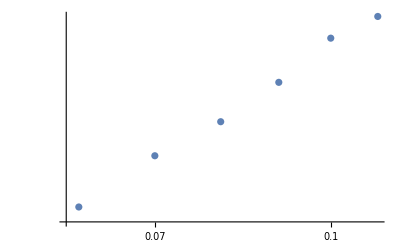

```mathematica
ListLogLogPlot[VfNo]
```

```mathematica
VfN=VfNo;
```

```mathematica
Clear[z];sol=FindFit[VfN,a z^b,{a,b},z]
```

{a→0.254278,b→0.213395}

```mathematica
f[z_]=a(z)^b/.sol
```

0.254278 z^0.213395

```mathematica
legends={"𝒱_∞ = 0.254(z-z_c)^0.21"};
```

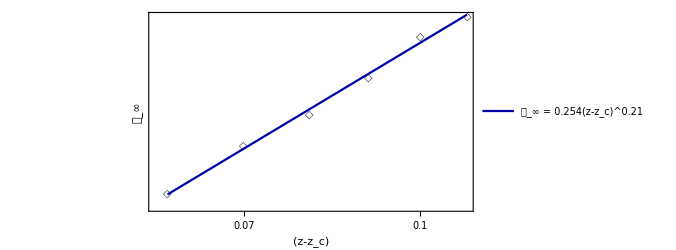

```mathematica
Show[{ListLogLogPlot[{VfNo},PlotMarkers->{"◇"},PlotStyle->GrayLevel[0.2],Frame->True,PlotRange->All,FrameStyle->Directive[Black,FontSize->16],FrameLabel->{Style["(z-z_c)",FontSize->17],Style["𝒱_∞",FontSize->17]},LabelStyle->Directive[Black,FontSize->19],AspectRatio->1/2,ImageSize->500],LogLogPlot[f[z],{z,0.06,0.11},LabelStyle->Directive[Darker[Blue],FontSize->16],PlotLegends->Placed[legends,{{0.7,0.25}}],PlotStyle->{Darker[Blue]}]}]
```